```mathematica
mtp={{0,0,0},{0,0,1},{1,0,1},{1,0,0},{1,1,0},{1,1,1},{1,1,1},{1,1,0}}
```

{{0,0,0},{0,0,1},{1,0,1},{1,0,0},{1,1,0},{1,1,1},{1,1,1},{1,1,0}}

```mathematica
currentStates=Reverse[IntegerDigits[#,2,3]&/@Range[0,7]]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

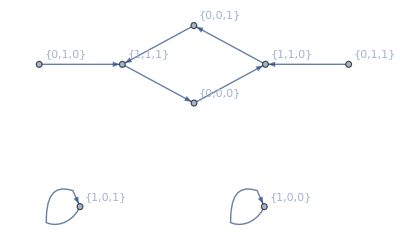

```mathematica
g1=Graph[Thread[currentStates->mtp],VertexLabels->"Name"]
```

## Re-labeling

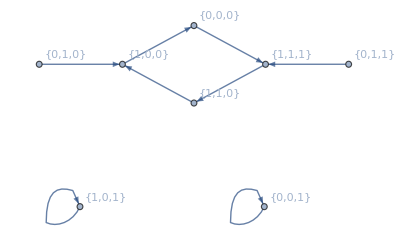

```mathematica
mtp2=ToExpression[StringReplace["[[1, 1, 0],
       [1, 0, 0],
       [1, 0, 1],
       [0, 0, 0],
       [1, 1, 1],
       [1, 0, 0],
       [0, 0, 1],
       [1, 1, 1]]",{"["->"{","]"->"}"}]];
g2=Graph[Thread[currentStates->mtp2],VertexLabels->"Name"]
```

```mathematica
IsomorphicGraphQ[g1,g2]
```

True

```mathematica
GroupOrder[GraphAutomorphismGroup[g1]]
```

4

```mathematica
GroupOrder[GraphAutomorphismGroup[g2]]
```

4

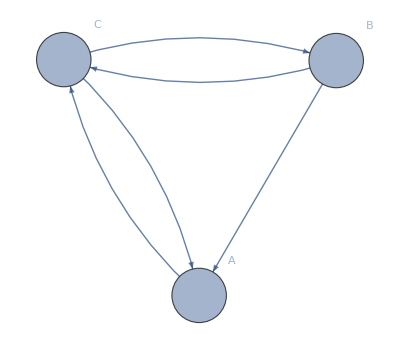

```mathematica
AdjacencyGraph[{{0,0,1},{1,0,1},{1,1,0}},VertexSize->Medium,VertexLabels->{1->"A",2->"B",3->"C"}]
```